# Test Transfer Matrices

## Definitions

```mathematica
<<PhysicalConstants`
<<Units`
```

```mathematica
Convert[Sqrt[VacuumPermeability/VacuumPermittivity],Ohm]//N
```

376.73 Ohm

```mathematica
Tgen=({{(1+p)Exp[-I n Cos[θ] k0 d], (1-p) Exp[-I n Cos[θ] k0 d]}, {(1-p) Exp[I n Cos[θ] k0 d], (1+p)Exp[I n Cos[θ] k0 d]}})/2
```

{{1/2 ⅇ^(-ⅈ d k0 n Cos[θ]) (1+p),1/2 ⅇ^(-ⅈ d k0 n Cos[θ]) (1-p)},{1/2 ⅇ^(ⅈ d k0 n Cos[θ]) (1-p),1/2 ⅇ^(ⅈ d k0 n Cos[θ]) (1+p)}}

This is the internal angle in a layer given an outside AOI in an ambient medium, assumed to be of index one:

```mathematica
IntAngle[θ_,n_]=ArcSin[Sin[θ]/n];
```

Matrices going from material 1 to material 2, plus propagation.

```mathematica
TTEk[d_,θ_,n2_,n1_,k0_]=Tgen/.{θ->θ2,n->n2}/.{p->(n1 Cos[θ1])/(n2 Cos[θ2])}/.{θ1->IntAngle[θ,n1],θ2->IntAngle[θ,n2]}
```

{{1/2 ⅇ^(-ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1+(n1 √(1-Sin[θ]^2/n1^2))/(n2 √(1-Sin[θ]^2/n2^2))),1/2 ⅇ^(-ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1-(n1 √(1-Sin[θ]^2/n1^2))/(n2 √(1-Sin[θ]^2/n2^2)))},{1/2 ⅇ^(ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1-(n1 √(1-Sin[θ]^2/n1^2))/(n2 √(1-Sin[θ]^2/n2^2))),1/2 ⅇ^(ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1+(n1 √(1-Sin[θ]^2/n1^2))/(n2 √(1-Sin[θ]^2/n2^2)))}}

```mathematica
TTMk[d_,θ_,n2_,n1_,k0_]=Tgen/.{θ->θ2,n->n2}/.{p->(n2 Cos[θ1])/(n1 Cos[θ2])}/.{θ1->IntAngle[θ,n1],θ2->IntAngle[θ,n2]}
```

{{1/2 ⅇ^(-ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1+(n2 √(1-Sin[θ]^2/n1^2))/(n1 √(1-Sin[θ]^2/n2^2))),1/2 ⅇ^(-ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1-(n2 √(1-Sin[θ]^2/n1^2))/(n1 √(1-Sin[θ]^2/n2^2)))},{1/2 ⅇ^(ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1-(n2 √(1-Sin[θ]^2/n1^2))/(n1 √(1-Sin[θ]^2/n2^2))),1/2 ⅇ^(ⅈ d k0 n2 √(1-Sin[θ]^2/n2^2)) (1+(n2 √(1-Sin[θ]^2/n1^2))/(n1 √(1-Sin[θ]^2/n2^2)))}}

```mathematica
Tgen/.{d->0,p->p[k]}
```

{{1/2 (1+p[k]),1/2 (1-p[k])},{1/2 (1-p[k]),1/2 (1+p[k])}}

```mathematica
NSell[As_,Bs_,λ_]:=Sqrt[1+Plus@@(As*λ^2/(λ^2-Bs))]
```

```mathematica
As={A1,A2};
Bs={B1,B2};
```

```mathematica
NSell[As,Bs,λ]
```

√(1+(A1 λ^2)/(-B1+λ^2)+(A2 λ^2)/(-B2+λ^2))

Need to replace the last element of the FS material...

```mathematica
SiAs={1.164011253};
SiBs={0.010834412};
NbAs={1.073359138,2.614422812};
NbBs={0.079542953,0.019906523};
FSAs={0.68374,0.42032, 0.5850};
FSBs={0.0046035,0.013397, 64.4930};
```

Let's see if we at least get the right answer for a simple normal incidence wave:

```mathematica
T1=TTEk[0,0,n2,n1,k]
```

{{1/2 (1+n1/n2),1/2 (1-n1/n2)},{1/2 (1-n1/n2),1/2 (1+n1/n2)}}

```mathematica
R1=-T1[[2,1]]/T1[[2,2]]//Simplify
```

(n1-n2)/(n1+n2)

## Two Layers

### Definitions

First layer SiO2, next Nb2O5, both from MLD data, substrate FS. The AIO will will 30 degrees, to make the analytical solution a bit cleaner. The first layer will be 100 nm, the second will be 200 nm.

```mathematica
krule=k0->2π/0.7
```

k0→8.97598

```mathematica
drules={d1->0.2,d2->0.3}
```

{d1→0.2,d2→0.3}

```mathematica
probrule={n2->NSell[SiAs,SiBs,λ],n1->NSell[NbAs,NbBs,λ],ns->NSell[FSAs,FSBs,λ],θ->30π/180}
```

{n2→√(1+(1.16401 λ^2)/(-0.0108344+λ^2)),n1→√(1+(1.07336 λ^2)/(-0.079543+λ^2)+(2.61442 λ^2)/(-0.0199065+λ^2)),ns→√(1+(0.585 λ^2)/(-64.493+λ^2)+(0.42032 λ^2)/(-0.013397+λ^2)+(0.68374 λ^2)/(-0.0046035+λ^2)),θ→π/6}

```mathematica
ltokrule=λ->2π/k0
```

λ→(2 π)/k0

```mathematica
ktolrule=k0->2π/λ
```

k0→(2 π)/λ

```mathematica
TTM=TTMk[0,θ,ns,n2,k0].TTMk[d2,θ,n2,n1,k0].TTMk[d1,θ,n1,1,k0]/.probrule;
TTE=TTEk[0,θ,ns,n2,k0].TTEk[d2,θ,n2,n1,k0].TTEk[d1,θ,n1,1,k0]/.probrule;
TTEfull=TTE/.ltokrule;
TTMfull=TTM/.ltokrule;
RTE=-TTEfull[[2,1]]/TTEfull[[2,2]];
RTM=-TTMfull[[2,1]]/TTMfull[[2,2]];
```

### Reflectivity

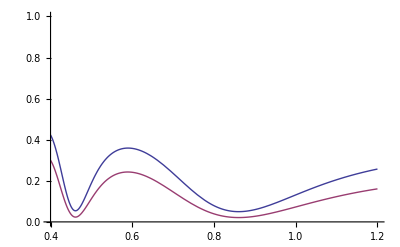

```mathematica
Plot[Evaluate[Abs[{RTE,RTM}]^2/.drules/.ktolrule],{λ,0.4,1.2},PlotRange->{0,1}]
```

```mathematica
Rcom=RTM/.drules/.krule;
Rmag=N[Abs[Rcom],20];
Rpow=N[Abs[Rcom]^2,20]
```

0.14589

### Group Delay

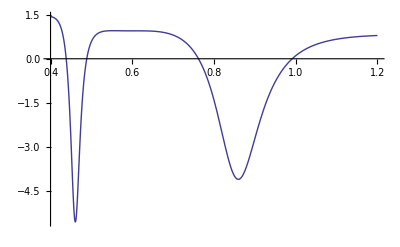

```mathematica
drdk=D[Evaluate[RTM/.drules],k0];
Rofk=RTM/.drules;
dphidw=(Re[Rofk]Im[drdk]-Im[Rofk]Re[drdk])/(Abs[Rofk]^2)/0.2997924580;
Plot[Evaluate[-dphidw/.ktolrule],{λ,0.4,1.2},PlotRange->All]
```

```mathematica
drdk=N[D[RTM,k0],16];
dphidw=-(Re[Rcom]Im[drdk]-Im[Rcom]Re[drdk])/(Abs[Rofk]^2)/0.2997924580;
dphidw/.krule/.drules
```

### Reflectivity Gradient

```mathematica
dr=D[Evaluate[RTM/.krule],d1]/.drules;
dR=N[2(Re[dr] Re[Rcom]+Im[dr] Im[Rcom]),20]
```

4.16835

```mathematica
dr2=D[Evaluate[RTM/.krule],d2]/.drules;
dR=N[2(Re[dr2] Re[Rcom]+Im[dr2] Im[Rcom]),20]
```

-0.0239045

### GD Gradient

```mathematica
dRgrad=D[drdk/.krule,d1]/.drules
```

-0.930531-6.12032 ⅈ

```mathematica
dTgrad=D[D[TTMfull,k0]/.krule,d1]/.drules
```

{{-6.89836+20.7409 ⅈ,2.04014-6.45518 ⅈ},{2.04014+6.45518 ⅈ,-6.89836-20.7409 ⅈ}}

```mathematica
dT=D[TTMfull,k0]/.krule/.drules
```

{{-1.09495-0.215873 ⅈ,0.356239+0.0870332 ⅈ},{0.356239-0.0870332 ⅈ,-1.09495+0.215873 ⅈ}}

```mathematica
dphi=(Im[dr] Re[Rcom]-Re[dr]Im[Rcom])/Rpow
```

-9.59568

```mathematica
dRdk=(Re[dr]Re[Rcom]+Im[dr]Im[Rcom])/Rmag
```

5.45658

```mathematica
dphigrad=(Im[ddR]Re[Rcom]-Re[ddR]Im[Rcom])/Rpow-(dphi dRdk+dR dphidw*0.299792458)/Rmag/.krule/.drules
```

121.113

## Three General Layers

```mathematica
Tsimp[p_,ϕ_]=({{(1+p)Exp[-I ϕ], (1-p) Exp[-I ϕ]}, {(1-p) Exp[I ϕ], (1+p)Exp[I ϕ]}})/2
```

{{1/2 ⅇ^(-ⅈ ϕ) (1+p),1/2 ⅇ^(-ⅈ ϕ) (1-p)},{1/2 ⅇ^(ⅈ ϕ) (1-p),1/2 ⅇ^(ⅈ ϕ) (1+p)}}

```mathematica
T=Tsimp[p23,ϕ3].Tsimp[p12,ϕ2].Tsimp[p01,ϕ1]
```

{{1/2 ⅇ^(ⅈ ϕ1) (1-p01) (1/4 ⅇ^(ⅈ ϕ2-ⅈ ϕ3) (1+p12) (1-p23)+1/4 ⅇ^(-ⅈ ϕ2-ⅈ ϕ3) (1-p12) (1+p23))+1/2 ⅇ^(-ⅈ ϕ1) (1+p01) (1/4 ⅇ^(ⅈ ϕ2-ⅈ ϕ3) (1-p12) (1-p23)+1/4 ⅇ^(-ⅈ ϕ2-ⅈ ϕ3) (1+p12) (1+p23)),1/2 ⅇ^(ⅈ ϕ1) (1+p01) (1/4 ⅇ^(ⅈ ϕ2-ⅈ ϕ3) (1+p12) (1-p23)+1/4 ⅇ^(-ⅈ ϕ2-ⅈ ϕ3) (1-p12) (1+p23))+1/2 ⅇ^(-ⅈ ϕ1) (1-p01) (1/4 ⅇ^(ⅈ ϕ2-ⅈ ϕ3) (1-p12) (1-p23)+1/4 ⅇ^(-ⅈ ϕ2-ⅈ ϕ3) (1+p12) (1+p23))},{1/2 ⅇ^(-ⅈ ϕ1) (1+p01) (1/4 ⅇ^(-ⅈ ϕ2+ⅈ ϕ3) (1+p12) (1-p23)+1/4 ⅇ^(ⅈ ϕ2+ⅈ ϕ3) (1-p12) (1+p23))+1/2 ⅇ^(ⅈ ϕ1) (1-p01) (1/4 ⅇ^(-ⅈ ϕ2+ⅈ ϕ3) (1-p12) (1-p23)+1/4 ⅇ^(ⅈ ϕ2+ⅈ ϕ3) (1+p12) (1+p23)),1/2 ⅇ^(-ⅈ ϕ1) (1-p01) (1/4 ⅇ^(-ⅈ ϕ2+ⅈ ϕ3) (1+p12) (1-p23)+1/4 ⅇ^(ⅈ ϕ2+ⅈ ϕ3) (1-p12) (1+p23))+1/2 ⅇ^(ⅈ ϕ1) (1+p01) (1/4 ⅇ^(-ⅈ ϕ2+ⅈ ϕ3) (1-p12) (1-p23)+1/4 ⅇ^(ⅈ ϕ2+ⅈ ϕ3) (1+p12) (1+p23))}}

```mathematica
Refl[T_]:=T[[1,2]]/T[[2,2]]
```

```mathematica
Simplify[ComplexExpand[Refl[T]*Conjugate[Refl[T]]]/.{Cos[x_]->c[x],Sin[y_]->s[y]},Element[{p12,p23,p01,ϕ1,ϕ2,ϕ3},Reals]]
```

(-4 (-1+p01^2) p12 (-1+p23^2) c[ϕ1] s[ϕ1] (c[ϕ2+ϕ3] s[ϕ2-ϕ3]+c[ϕ2-ϕ3] s[ϕ2+ϕ3])+s[ϕ1]^2 ((p01+p12)^2 (-1+p23)^2 c[ϕ2-ϕ3]^2-2 (p01^2-p12^2) (-1+p23^2) c[ϕ2-ϕ3] c[ϕ2+ϕ3]+(p01-p12)^2 (1+p23)^2 c[ϕ2+ϕ3]^2+((p01+p12) (-1+p23) s[ϕ2-ϕ3]+(p01-p12) (1+p23) s[ϕ2+ϕ3])^2)+c[ϕ1]^2 ((1+p01 p12)^2 (-1+p23)^2 c[ϕ2-ϕ3]^2+2 (-1+p01^2 p12^2) (-1+p23^2) c[ϕ2-ϕ3] c[ϕ2+ϕ3]+(-1+p01 p12)^2 (1+p23)^2 c[ϕ2+ϕ3]^2+((1+p01 p12) (-1+p23) s[ϕ2-ϕ3]-(-1+p01 p12) (1+p23) s[ϕ2+ϕ3])^2))/(-4 (-1+p01^2) p12 (-1+p23^2) c[ϕ1] s[ϕ1] (c[ϕ2+ϕ3] s[ϕ2-ϕ3]+c[ϕ2-ϕ3] s[ϕ2+ϕ3])+s[ϕ1]^2 ((p01-p12)^2 (-1+p23)^2 c[ϕ2-ϕ3]^2-2 (p01^2-p12^2) (-1+p23^2) c[ϕ2-ϕ3] c[ϕ2+ϕ3]+(p01+p12)^2 (1+p23)^2 c[ϕ2+ϕ3]^2+((p01-p12) (-1+p23) s[ϕ2-ϕ3]+(p01+p12) (1+p23) s[ϕ2+ϕ3])^2)+c[ϕ1]^2 ((-1+p01 p12)^2 (-1+p23)^2 c[ϕ2-ϕ3]^2+2 (-1+p01^2 p12^2) (-1+p23^2) c[ϕ2-ϕ3] c[ϕ2+ϕ3]+(1+p01 p12)^2 (1+p23)^2 c[ϕ2+ϕ3]^2+((-1+p01 p12) (-1+p23) s[ϕ2-ϕ3]-(1+p01 p12) (1+p23) s[ϕ2+ϕ3])^2))